# Resonance Accelerator

```mathematica
(* a circular accelerator composite of 2 semi-cirular plate, with different voltage, a B-field is applied along the axis on motion *)
```

```mathematica
(* The centrapatal force on the electron *)
m v^2/r= q v×B = q v B
(m v)/(q B)= r
v = q/m r B
```

```mathematica
(* The time for a half circule is *)
Subscript[t, h]= (π r)/v= (π m)/(B q)
```

```mathematica
(* The velocity gain in each half period is *)
1/2 m (v + Δv)^2-1/2 m v^2=q V
2 v Δv + (Δv)^2=2 q/m V
```

```mathematica
Array[v,20];
Array[r,20];
Array[
```

```mathematica
V=2;
B=2;
v[1]= 2 V;
r[1]= v[1]/B;
Table[{ v[i]=√(2V + v[i-1]^2),r[i]=v[i]/B},{i,2,20}];
vList = Table[v[i]//N,{i,1,20}]
rList = Table[r[i]//N,{i,1,20}]
```

{4.,4.47214,4.89898,5.2915,5.65685,6.,6.32456,6.63325,6.9282,7.2111,7.48331,7.74597,8.,8.24621,8.48528,8.7178,8.94427,9.16515,9.38083,9.59166}

{2.,2.23607,2.44949,2.64575,2.82843,3.,3.16228,3.31662,3.4641,3.60555,3.74166,3.87298,4.,4.12311,4.24264,4.3589,4.47214,4.58258,4.69042,4.79583}

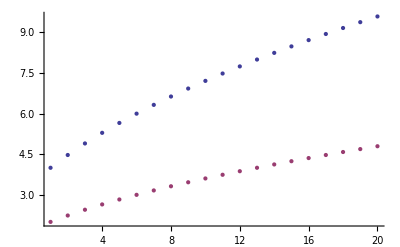

```mathematica
ListPlot[{vList,rList}]
```